## Задача 4. Дадена е началната задача за ОДУ y’=y-(a+1)sinx, y(0)=b, x∈[0; 0.5], където a=0, b=3

## а) По метода на Ойлер да се реши приближено задачата като целия интервал се раздели на a+b+3 = 0+3+3 = 6 равни части. Запишете резултатите в таблица. Може да се запишат само първите 2 и последните 2 реда от таблицата.

```mathematica
Clear[x,y]
DSolve[{y'[x]== y[x] - Sin[x], y[0] == 3}, y[x],x]
```

{{y[x]→1/2 (5 ⅇ^x+Cos[x]+Sin[x])}}

Визуализация на точното решение:

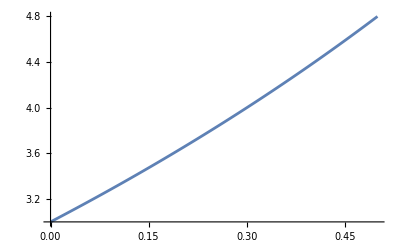

```mathematica
yt[x_]:=1/2 (5 ⅇ^x+Cos[x]+Sin[x])
Plot[yt[x],{x,0,0.5}]
```

Мрежата е с n = 6 и стъпка h = 0.0833333

Теоретичната локална  грешка е 0.00694444

Теоретичната глобална грешка е 0.0833333

i = 0 x_i = 0. y_i = 3. f_i = 3. y_точно = 3. истинска грешка = 0.

i = 1 x_i = 0.0833333 y_i = 3.25 f_i = 3.16676 y_точно = 3.25714 истинска грешка = 0.00714348

i = 2 x_i = 0.166667 y_i = 3.5139 f_i = 3.348 y_точно = 3.52942 истинска грешка = 0.0155238

i = 3 x_i = 0.25 y_i = 3.7929 f_i = 3.54549 y_точно = 3.81822 истинска грешка = 0.0253247

i = 4 x_i = 0.333333 y_i = 4.08835 f_i = 3.76116 y_точно = 4.12511 истинска грешка = 0.0367521

i = 5 x_i = 0.416667 y_i = 4.40178 f_i = 3.99707 y_точно = 4.45182 истинска грешка = 0.0500361

i = 6 x_i = 0.5 y_i = 4.73487 f_i = 4.25545 y_точно = 4.80031 истинска грешка = 0.0654333

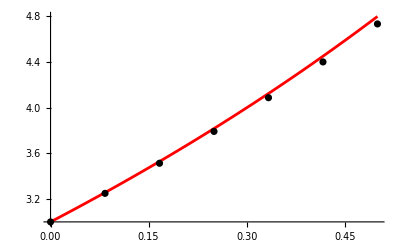

```mathematica
(*въвеждаме условието на задачата*)
a = 0.; b = 0.5;
x = a;
y = 3.;
points = {{x,y}};
f[x_,y_]:=y - Sin[x]
(*точно решение*)
yt[x_]:=1/2 (5 ⅇ^x+Cos[x]+Sin[x])
(*съставяме мрежата*)
n=6; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^2]
Print["Теоретичната глобална грешка е ", h]
(*намираме неизвестните стойности за Subscript[y, i]*)
For[i = 0, i<= n, i++,
Print["i = ", i, " x_i = ",x, " y_i = ",y, " f_i = ",f[x,y], " y_(:0442:043e:0447:043d:043e) = ", yt[x], " истинска грешка = ", Abs[y-yt[x]]];
y = y+h*f[x,y];
x=x+h;
AppendTo[points,{x,y}]
]
(*визуализация на резултатите*)
gryt = Plot[yt[x],{x,a,b}, PlotStyle->Red];
grp = ListPlot[points, PlotStyle->Black];
Show[gryt,grp]
```

Отговор: Приближените решения са y_i.

## б) Каква е точността на полученото решение?

Отговор: Теоретичната глобална грешка е O(h) = 0.0833333

## в) С колко знака се представя крайният резултат и с колко знака е необходимо да извършваме междинните изчисления?

Отговор: Крайният резултат се представя с 4 знака, тъй като теоретичната локална  грешка е O(h^2) и стъпката е h = 0.0294118. Междинните пресмятания е необходимо да извършваме с 5 знака.

## г) Може ли да се намери точно решение на задачата? Ако да - сравнете приближеното и точното решение.

Отговор: Да се препише точното решение на задачата, y_точно и истинската грешка.

## д) Каква би била точността при използване на модифицирания метод на Ойлер за поставената задача със същата стъпка? Сравнете точностите на двата метода.

```mathematica
(*въвеждаме условието на задачата*)
a = 0.; b = 0.5;
x = a;
y = 3.;
points = {{x,y}};
f[x_,y_]:=y - Sin[x]
(*точно решение*)
yt[x_]:=1/2 (5 ⅇ^x+Cos[x]+Sin[x])
(*съставяме мрежата*)
n=6; h = (b-a)/n;
Print["Мрежата е с n = ", n, " и стъпка h = ", h]
(*Изчисляваме теоретичната грешка*)
Print["Теоретичната локална  грешка е ", h^3]
Print["Теоретичната глобална грешка е ", h^2]
```

Мрежата е с n = 6 и стъпка h = 0.0833333

Теоретичната локална  грешка е 0.000578704

Теоретичната глобална грешка е 0.00694444

Отговор: Теоретичната глобална грешка е 0.00694444. Тъй като грешката на модифицирания метод на Ойлер е по-малка от тази на метода на Ойлер, то той е по-точен.